# Dipole’s emission near sphere

Zhaohua Tian

2020 10 14

## Theoretical Expression

The detailed informations can be found here

[Dipole's Emission Near Sphere](https://knifelees3.github.io/2020/06/20/A_En_DipoleEmissionNearSphere/)

The normalized decay rate is  as follows

Γ_t^⊥/Γ_0=1+3/2 Re∑_(l=1)^∞ (2l+1)l(l+1)b_l((h_l^(1)(k_b r))/(k_b r))^2

Γ_r^⊥/Γ_0=3/2∑_(l=1)^∞ (2l+1)l(l+1)|(j_l^(1)(k_b r)+b_l h_l^(1)(k_b r))/(k_b r)|^2

Γ_t^∥/Γ_0=1+3/2 Re(∑_(l=1)^∞ (l+1/2)[b_l((ξ'_l(k_b r))/(k_b r))^2+a_l(h_l^(1)(k_b r))^2)

Γ_r^∥/Γ_0=3/4∑_(l=1)^∞ (2l+1)[|j_l(k_b r)+a_l h_l^(1)(k_b r)|^2+(|(ψ'(k_b r)+b_l ξ'_l(k_b r))/(k_b r)|)^2]

With

a_n=(μ_b n_s^2 j_n(k_s r_s)[k_b r_s j_n(k_b r_s)]'−μ_s j_n(k_b r_s)[k_s r_s j_n(k_s r_s)]')/(μ_b n_s^2 j_n(k_s r_s)[k_b r_s h_n^(1)(k_b r_s)]'−μ_s h_n^(1)(k_b r_s)[k_s r_s j_n(k_s r_s)]')

b_n=(μ_s j_n(k_s r_s)[k_b r_s j_n(k_b r_s)]'−μ_b j_n(k_b r_s)[k_s r_s j_n(k_s r_s)]')/(μ_s j_n(k_s r_s)[k_b r_s h_n^(1)(k_b r_s)]'−μ_b h_n^(1)(k_b r_s)[k_s r_s j_n(k_s r_s)]')

ξ_l(x)=x h_n^(1)(x)

ψ_l(x)=x j_n(x)

r=d+r_s

k_b=n_b k_0
k_s=b_s k_0  
with n_b the refractive index of embedding medium and n_s the refractive index of sphere.

## Realizations in Mathematica

### The dispersion model function

There are three models from Prof. Chen, Fitted by Cicy and used by Wei Yan. The function definition can be found here

Dispersion Function Link

### The function to calculate the electric power

I have written the functions here

Functions for Decay Rate Calculations

Then we can test the functions

```mathematica
num=200;
nm=10^(-9);
λmat=Subdivide[300,580,num]*nm;
nb=1;
nsChen=N[√DispersionAu[λmat]];
nsCiCy=N[√DispersionAuCiCy[λmat]];
nsYan=N[√DispersionAuYan[λmat]];
r0=40*nm;
dis=r0+10*nm;
nP1=nPnearSphere[λmat,nb,nsChen,r0,dis];
nP2=nPnearSphere[λmat,nb,nsCiCy,r0,dis];
nP3=nPnearSphere[λmat,nb,nsYan,r0,dis];
```

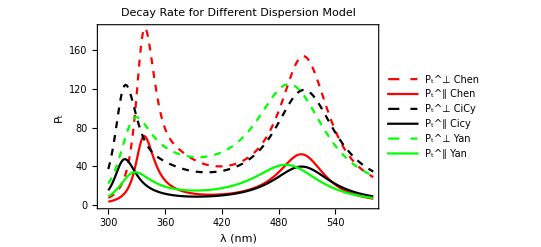

```mathematica
ListPlot[{Thread[{λmat/nm,nP1[[1,All]]}],Thread[{λmat/nm,nP1[[2,All]]}],
Thread[{λmat/nm,nP2[[1,All]]}],Thread[{λmat/nm,nP2[[2,All]]}],
Thread[{λmat/nm,nP3[[1,All]]}],Thread[{λmat/nm,nP3[[2,All]]}]},Joined->True,Frame->True,FrameLabel->{"λ (nm)","P_t"},PlotLegends->{"P_t^⊥ Chen","P_t^∥ Chen","P_t^⊥ CiCy","P_t^∥ Cicy","P_t^⊥ Yan","P_t^∥ Yan"},PlotRange->Full
,PlotStyle->{Directive[Red,Dashed],Red,Directive[Black,Dashed],Black,Directive[Green,Dashed],Green},PlotLabel->"Decay Rate for Different Dispersion Model"]
```

```mathematica
nPnearSphere[604*10^(-9),1,0.150407+2.98107*ⅈ,40*10^(-9),54*10^(-9)]
```

{20.2615,4.24986}

## List of initialized functions

### Initialize function

```mathematica
SetOptions[EvaluationNotebook[],FrontEnd`ReturnCreatesNewCell->False]
jet[u_?NumericQ]:=Blend[{{0,RGBColor[0,0,9/16]},{1/9,Blue},{23/63,Cyan},{13/21,Yellow},{47/63,Orange},{55/63,Red},{1,RGBColor[1/2,0,0]}},u]/;0≤u≤1
meshgrid[x_List,y_List]:={ConstantArray[x,Length[y]],Transpose@ConstantArray[y,Length[x]]};
```

### Dispersion functions

```mathematica
DispersionAu[λ_]:=Module[{ϵinf=5.90157,c=3*10^8,ωD=1.297056*10^16,γD=4.108244*10^13,
ωL=4.298305*10^15,Δϵ=1.26913,ω0L=4.298305*10^15,γL=0.374*10^15,ω,ϵ},
ω=(2*π)/λ*c;ϵ=ϵinf-Δϵ ωL^2/(ω^2-ω0L^2+2ⅈ*ω*γL)-ωD^2/(ω^2+ⅈ*ω*γD)];
DispersionAuCiCy[λ_]:=Module[{ϵinf=5.90157,c=3*10^8,ωD=5.56623*10^15,γD=1.121138*10^14,
ωL=2.396346*10^15,ω0L=4.4000041*10^15,γL=9.370830*10^14,ω,ϵ},
ω=(2*π)/λ*c;ϵ=ϵinf(1-ωL^2/(ω^2-ω0L^2+ⅈ*ω*γL)-ωD^2/(ω^2+ⅈ*ω*γD))];
DispersionAuYan[λ_]:=Module[{ϵinf=6,c=3*10^8,ωD=5.37*10^15,γD=6.216*10^13,
ωL=2.2636*10^15,ω0L=4.572*10^15,γL=1.332*10^15,ω,ϵ},
ω=(2*π)/λ*c;ϵ=ϵinf(1-ωL^2/(ω^2-ω0L^2+ⅈ*ω*γL)-ωD^2/(ω^2+ⅈ*ω*γD))];
```

### Decay rate calculating functions

```mathematica
nPnearSphere[λ_,nb_,ns_,r0_,dis_,radiative_:0]:=Module[{num=50,k0,kb,ks,kbr0,ksr0,kbr,a,b,DSphJ,DSphH,pRad,pTange,pRadradiative,
pTangeradiative},k0=N[(2*π)/λ];kb=k0*nb;ks=k0*ns;
kbr0=kb*r0;ksr0=ks*r0;kbr=kb*dis;
(*The derivative*)
DSphJ[l_,x_]:=SphericalBesselJ[l,x]/2+x/2*(SphericalBesselJ[l-1,x]-SphericalBesselJ[l+1,x]);
DSphH[l_,x_]:=SphericalHankelH1[l,x]/2+x/2*(SphericalHankelH1[l-1,x]-SphericalHankelH1[l+1,x]);
(* The Mie Scattering Coefficients*)
b[l_]:=N[-(ns^2*SphericalBesselJ[l,ksr0]*DSphJ[l,kbr0]-SphericalBesselJ[l,kbr0]*DSphJ[l,ksr0])/(ns^2*SphericalBesselJ[l,ksr0]*DSphH[l,kbr0]-SphericalHankelH1[l,kbr0]*DSphJ[l,ksr0])];
a[l_]:=N[-(SphericalBesselJ[l,ksr0]*DSphJ[l,kbr0]-SphericalBesselJ[l,kbr0]*DSphJ[l,ksr0])/(SphericalBesselJ[l,ksr0]*DSphH[l,kbr0]-SphericalHankelH1[l,kbr0]*DSphJ[l,ksr0])];
pRad=1.5*Re[Total[Table[N[(2*m+1)*m*(m+1)*b[m]*(SphericalHankelH1[m,kbr]/kbr)^2],{m,1,num}]]]+1;
pTange=1.5*Re[Total[Table[N[(m+1/2)*(b[m]*(DSphH[m,kbr]/kbr)^2+a[m]*(SphericalHankelH1[m,kbr])^2)],{m,1,num}]]]+1;
If[radiative==0,
Return[{pRad,pTange}];,
(pRadradiative=1.5*Total[Table[N[(2*m+1)*m*(m+1)
*Abs[(SphericalBesselJ[m,kbr]+b[m]*SphericalHankelH1[m,kbr])/kbr]^2],{m,1,num}]];
pTangeradiative=0.75*Total[Table[N[(2*m+1)*(Abs[SphericalBesselJ[m,kbr]+a[m]*SphericalHankelH1[m,kbr]]^2+
Abs[(DSphJ[m,kbr]+b[m]*DSphH[m,kbr])/kbr]^2)],{m,1,num}]];Return[{pRad,pTange,pRadradiative,pTangeradiative}])];

]
```

### Position projection function

```mathematica
posProj[pos_,p_]:=Module[{dis,αrad,αtange},
dis=√(Abs[pos[[1]]]^2+Abs[pos[[2]]]^2+Abs[pos[[3]]]^2);
αrad=Abs[pos[[1]]*p[[1]]+pos[[2]]*p[[2]]+pos[[3]]*p[[3]]]/dis;
αtange=N[√(1-αrad^2)];
Return[{αrad,αtange}];
];
```

We can give a simple test here

```mathematica
dipole[θ_,ϕ_]:={Sin[θ]*Cos[ϕ],Sin[θ]*Sin[ϕ],Cos[θ]};
postionSph[r_,θ_,ϕ_]:={Sin[θ]*Cos[ϕ],Sin[θ]*Sin[ϕ],Cos[θ]};
N[dipole[π/2,0].postionSph[1,π/2,π/2]]
```

0.

### Decay Rate for radius and dipole

The function to give the dipole moment and decay rate for a specific dipole

```mathematica
dipole[θ_,ϕ_]:={Sin[θ]*Cos[ϕ],Sin[θ]*Sin[ϕ],Cos[θ]};
dipole2D[θ_,ϕ_]:={{-Cos[θ]*Cos[ϕ],-Cos[θ]*Sin[ϕ],Sin[θ]},{Sin[ϕ],-Cos[ϕ],0}};
dipole3D[α_,β_,ϕx_,ϕy_,ϕz_]:=Module[{rotFun,dx,dy,dz,norm,rotmat,d1,d2,d3},
rotmat=N[RotationMatrix[ϕz,{0,0,1}].RotationMatrix[ϕy,{0,1,0}].RotationMatrix[ϕx,{1,0,0}]];

dx=N[{1,0,0}];
dy=N[{0,α,0}];
dz=N[{0,0,β}];

norm=N[√(1+α^2+β^2)];
d1=N[rotmat.dx/norm];
d2=N[rotmat.dy/norm];
d3=N[rotmat.dz/norm];
Return[{d1,d2,d3}]];


postionSph[r_,θ_,ϕ_]:=r*{Sin[θ]*Cos[ϕ],Sin[θ]*Sin[ϕ],Cos[θ]};

Decay1D[r0_,dis_,radiative_:0]:=Module[{nb,ns,λ,nm,nP},
nm=10^(-9);
λ=N[655*nm];
nb=1;
ns=N[√DispersionAuYan[λ]];
nP=nPnearSphere[λ,nb,ns,r0,dis,radiative]];
```

The function for calculating 1D, 2D, 3D dipole

```mathematica
Decay1DPattern[nP_,p_,θ_,ϕ_]:=Module[{nm,λ,nb,ns,α,nPList,rvec,β},
nm=10^(-9);
rvec=postionSph[1,θ,ϕ];
α=rvec.p;
β=√(1-α^2);
nPList=N[α^2*nP[[1]]+β^2*nP[[2]]]];'


Decay2DPattern[nP_,p2D_,θ_,ϕ_]:=Module[{nm,λ,nb,ns,α1,α2,nPList,rvec,β1,β2,p1,p2},
nm=10^(-9);
rvec=postionSph[1,θ,ϕ];
p1=p2D[[1]];
p2=p2D[[2]];
α1=Abs[rvec.p1];
β1=√(Total[Abs[p1]^2]-α1^2);
α2=Abs[rvec.p2];
β2=√(Total[Abs[p2]^2]-α2^2);
nPList=N[(α1^2+α2^2)*nP[[1]]+(β1^2+β2^2)*nP[[2]]]];
Decay3DPattern[nP_,p3D_,θ_,ϕ_]:=Module[{nm,λ,nb,ns,α1,α2,α3,nPList,rvec,β1,β2,β3,p1,p2,p3},
nm=10^(-9);
rvec=postionSph[1,θ,ϕ];
p1=p3D[[1]];
p2=p3D[[2]];
p3=p3D[[3]];
α1=rvec.p1;
β1=√(Total[Abs[p1]^2]-α1^2);
α2=rvec.p2;
β2=√(Total[Abs[p2]^2]-α2^2);
α3=rvec.p3;
β3=√(Total[Abs[p3]^2]-α3^2);
nPList=N[(α1^2+α2^2+α3^2)*nP[[1]]+(β1^2+β2^2+β3^2)*nP[[2]]]];
```

Null'